# EDMD LSA

## Flow

Constraints - done

Initialize disks randomly obeying constraints - done

initialize velocities - done

assign disks to cells - done

Find next event for all disks (once; beginning) not done

Find next event for sphere i

Find next collision for sphere i

checks events of collision partner to keep collisions symmetric

predict collision time for pair ij - done

Return next event (minHeap implementation)

Process collision - done

Process Transfer, boundary events

Update cell of disk to time

## Constraints

### overlapC

#### Definitions

```mathematica
overlapC[{{x1_, y1_}, r1_}, {{x2_, y2_}, r2_}]:=
((r2+r1)^2≤(y2-y1)^2+(x2-x1)^2)
```

#### Testing

```mathematica
overlapC[{{1,1},1}, {{0,0},.5}]
```

False

### borderC

#### Definitions

```mathematica
borderC[{x_, y_}, r_, size_]:=And[
size-r≥x, size-r≥y,r≤x, r≤y
]
```

#### Testing

```mathematica
borderC[{1,1},1, 2]
```

True

## Initialization

### createDisk

Randomly obtains disk coordinates that satisfy constraints.

#### Definition

```mathematica
createDisk[circles_List,radii_List, size_]:=Module[
{cnumber=circles//Length, position, riffled, count=0, insert=False, rc, r},

(*splice radii list, select next*)
rc=radii⟦;;cnumber⟧;
r=radii⟦cnumber+1⟧;
riffled=Riffle[circles,rc];

While[And[count<100, !insert ],
	position=RandomReal[{0, size}, 2];

	If[And[
	borderC[position,r,size],
	And@@(overlapC[{position, r}, #]&/@riffled)
	],
	insert=True;
	];
count=count+1;
];
position
]
```

#### testing

```mathematica
createDisk[{{1,1}, {2,2}}, {.5,.4, 1}, 3]
```

{0.0516464,-1.55097}

### createDisks

Randomly generates initial coordinates for the set of radii.

#### Definitions

```mathematica
createDisks[radii_List, size_]:=Module[
{coordinates, number=radii//Length},
coordinates=createDisk[{}, radii, size];
NestList[Join@createDisk[#, radii, size]&, coordinates, number-1]
]
```

#### testing

```mathematica
createDisks[{1,1,1}, 5]
```

{{3.13005,3.61477},{1.70887,-0.472914},{-1.7051,0.747208}}

### velocityInit

#### Definitions

```mathematica
velocityInit[size_,number_]:=RandomReal[size{-1, 1}, number]
```

#### Testing

```mathematica
velocityInit[5]
```

{-0.868833,-0.560377,-0.0372914,0.866285,0.197821}

### setInitialEvents

Initializing all events to checks. Events are defined by triples: {timestamp, i, j}. Need to insert into minHeap still.

#### Definitions

```mathematica
setInitialEvents[N_,H_, gtime_:0]:=Block[
{events},
events=Table[{gtime, i, Infinity}, {i, N}];
]
```

## Cell Method

### binCenters

#### Definition

Consider nrows even.

```mathematica
binCenters[nrows_, size_]:=With[{step=size/nrows},
Table[step{i, j}/2, {i, 1, 2nrows,2}, {j, 1, 2nrows,2}]
]
```

#### Testing

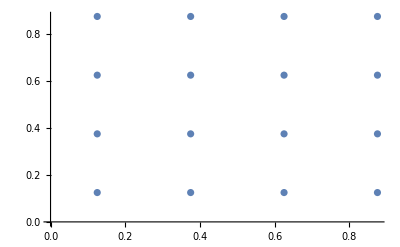

```mathematica
binCenters[4,1 ]//Flatten//Partition[#,2]&//ListPlot
```

### nearestCells

Maps list of coordinates to matrix of bins by index

#### Definition

```mathematica
nearestCells[coordinates_, nrows_, size_]:=Module[
{nf=Nearest[coordinates->Range@Length@coordinates, DistanceFunction->ChessboardDistance], coordinatemat},
nf[binCenters[nrows, size], {Infinity, size/(2 nrows)}]
]
```

#### Testing

```mathematica
data=RandomReal[10, {50, 2}];
```

```mathematica
m=nearestCells[data, 4, 10]
```

{{{42,47},{},{27,25,5},{24,16}},{{},{4,35,40,18,14,31},{23,6,20,7,10,26,46,22},{19,32,43}},{{13,30,36,1},{39,29},{3,37,48},{49,34}},{{11,50,41,15,38,17},{28,9},{8,12},{2,45,21,44,33}}}

```mathematica
Association[Flatten[MapIndexed[Function[{list,pos},#->pos&/@list],m,{2}]]]
```

<|42→{1,1},47→{1,1},27→{1,3},25→{1,3},5→{1,3},24→{1,4},16→{1,4},4→{2,2},35→{2,2},40→{2,2},18→{2,2},14→{2,2},31→{2,2},23→{2,3},6→{2,3},20→{2,3},7→{2,3},10→{2,3},26→{2,3},46→{2,3},22→{2,3},19→{2,4},32→{2,4},43→{2,4},13→{3,1},30→{3,1},36→{3,1},1→{3,1},39→{3,2},29→{3,2},3→{3,3},37→{3,3},48→{3,3},49→{3,4},34→{3,4},11→{4,1},50→{4,1},41→{4,1},15→{4,1},38→{4,1},17→{4,1},28→{4,2},9→{4,2},8→{4,3},12→{4,3},2→{4,4},45→{4,4},21→{4,4},44→{4,4},33→{4,4}|>

```mathematica
binCenters[4,10];
```

```mathematica
m
```

50

```mathematica
m
```

{{{},{{0.805173,3.31452},{0.883983,4.40272},{1.65688,4.40467},{1.96505,3.78695}},{{1.806,6.42057},{2.14145,6.03385}},{{0.65088,8.88589},{0.797013,9.64187}}},{{{3.97731,1.4623},{3.0372,1.25763},{4.48522,1.07146},{4.64892,1.99548}},{{3.75446,3.25761},{4.50227,2.76267}},{{3.62191,5.63893},{4.46167,6.02467},{3.27454,7.01114}},{{3.79164,8.58965}}},{{{5.37395,0.752036},{5.8744,0.284669}},{},{{6.5581,5.46856},{7.15174,6.77586},{7.1897,5.49383}},{{6.92188,9.30649}}},{{{8.30408,1.48281},{8.74998,0.340356}},{{8.62647,3.73118},{8.36794,4.24888},{9.57911,3.66747},{9.42693,4.64879}},{{8.77438,6.21068},{8.0161,6.8461},{9.68578,6.45644}},{{9.45638,8.76425}}}}

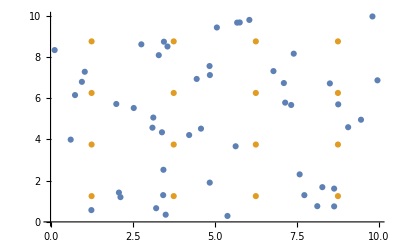

```mathematica
ListPlot[{data, binCenters[4, 10]//Flatten[#, 1]&}]
```

### cellMap

Maps disk coordinate to bin. For convenience, consider even number of bins. Denote nbins as the number of rows of squares.

#### Definition

```mathematica
cellMap[coordinate_, size_, nrows_]:=With[{step=size/nrows},
Ceiling[(coordinate)/step]
]
```

#### Testing

Note that particles won’t overlap boundary, so no edge cases.

```mathematica
cellMap[{0,2}, 5, 9]
```

{0,4}

### cellA

This function will invert cellMat into a association, where each index i maps to the current cell corresponding to coordinate i.

#### Definition

```mathematica
cellA[cellMat_]:=Association[Flatten[
MapIndexed[Function[{list, pos}, # ->pos &/@list],
cellMat,
{2}]]]
```

#### Testing

```mathematica
data=RandomReal[10, {50, 2}];
m=nearestCells[data, 4, 10];
a=cellA[m]
```

<|4→{1,1},19→{1,1},44→{1,1},29→{1,2},27→{1,2},20→{1,2},8→{1,3},32→{1,3},7→{1,3},47→{1,4},24→{1,4},37→{2,1},49→{2,1},34→{2,1},21→{2,1},48→{2,1},46→{2,2},40→{2,2},13→{2,2},25→{2,2},12→{2,2},31→{2,2},6→{2,3},43→{2,3},9→{2,4},33→{2,4},15→{2,4},26→{2,4},18→{2,4},42→{2,4},22→{3,1},41→{3,1},30→{3,2},14→{3,2},17→{3,2},38→{3,2},3→{3,3},2→{4,1},16→{4,1},28→{4,2},35→{4,2},1→{4,2},36→{4,2},39→{4,3},45→{4,3},23→{4,3},10→{4,4},5→{4,4},50→{4,4},11→{4,4}|>

```mathematica
a[1]
```

{2,3}

```mathematica
a⟦1⟧
```

{1,1}

### findNeighbors

Returns list of indices, corresponding to possible collision pairs. Defined through maximum of 8 neighboring cells, as well as current cells. Note that includes itself

#### Definition

```mathematica
findNeighbors[cellMatrix_, cellindex_, nrows_]:=Module[
{i, j, currentlist, cl, ck, l, k},
(*particle cell & initialization*)
{i, j}=cellindex;
currentlist={};
(*iteration through cells, eliminating edge cases*)
For[k=-1, k<2, k++,
ck=cellindex⟦1⟧+k;
If[ck≤ nrows && ck≥1,
For[l=-1, l<2, l++,
cl=cellindex⟦2⟧+l;
If[cl≤ nrows && cl≥1,
currentlist=Join[currentlist, cellMatrix⟦ck, cl⟧];
]]]];
currentlist
]
```

#### Testing

```mathematica
data=RandomReal[10, {50, 2}];
m=nearestCells[data, 4, 10];
```

```mathematica
a=cellA[m];
a[[1]]
```

{1,1}

```mathematica
findNeighbors[m, a⟦1⟧, 4]//Length
```

9

### updateCell

#### Definition

```mathematica
updateCell=Function[{i, coordinates, cellA, cellMat, size, nrows},
Module[
{currentk, currentj, oldk, oldj},
(*initialize variables*)
{currentk, currentj}=cellMap[coordinates⟦i⟧, size, nrows];
{oldk, oldj}=cellA[i];
(*delete and reinsert element from cellMat*)
cellMat⟦oldk, oldj⟧=Select[cellMat⟦oldk, oldj⟧, #≠i&];
AppendTo[cellMat⟦currentk, currentj⟧, {i}];
(*reset element in association*)
cellA[i]={currentk, currentj};
],
HoldAll
];
```

#### Testing

```mathematica
coordinates=RandomReal[10, {50, 2}];
m=nearestCells[coordinates, 4, 10];
a=cellA[m]
```

<|20→{1,1},22→{1,1},49→{1,1},1→{1,1},26→{1,2},36→{1,2},24→{1,2},32→{1,2},21→{1,2},17→{1,3},11→{1,3},19→{1,3},39→{1,3},18→{1,3},42→{1,4},6→{1,4},28→{1,4},41→{2,1},15→{2,1},40→{2,1},13→{2,1},31→{2,1},10→{2,2},47→{2,2},33→{2,2},29→{2,2},30→{2,3},46→{2,3},43→{2,4},27→{3,1},44→{3,1},50→{3,1},45→{3,1},8→{3,2},12→{3,2},9→{3,2},23→{3,3},38→{3,3},35→{3,3},25→{3,4},2→{3,4},16→{4,1},48→{4,1},7→{4,1},5→{4,1},4→{4,2},37→{4,4},3→{4,4},34→{4,4},14→{4,4}|>

```mathematica
a[1]
```

{2,3}

```mathematica
coordinates⟦1⟧={9,9}
```

{9,9}

```mathematica
updateCell[1, coordinates, a, m, 10, 4]
```

1111

```mathematica
a[1]
```

{1,1}

```mathematica
a[1]
```

{3,3}

## Min Heap Implementation

I will implement a min-Heap using a list a. The Heap will store tuples {t, i}, where t is the time of the next collision including particle i.

### HeapQ

Tests if a is a min-Heap in O(N).

#### Definition

```mathematica
HeapQ[a_List]:=Module[{n=a//Length},
And@@Table[a⟦Floor[i/2]⟧⟦1⟧≤ a⟦i⟧⟦1⟧, {i, 2, n}]
]
```

#### Testing

```mathematica
a=Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
HeapQ[a]
```

True

### HSwap

#### Definition

Function swaps elements i and j of list a. Argument a has to be in variable (unevaluated) form

```mathematica
HSwap=Function[{a, i, j},
{a⟦i⟧, a⟦j⟧}={a⟦j⟧, a⟦i⟧};
a,
HoldFirst];
```

#### Testing

```mathematica
x={1, 2, 3}
HSwap[x,1,3]
```

{1,2,3}

{3,2,1}

```mathematica
Clear[a, i, j]
```

```mathematica
a={1,2,3,4,5}
```

{1,2,3,4,5}

```mathematica
a[[1]]=a[[4]]
```

4

```mathematica
a[[1]]
```

4

```mathematica
HSwap[a, 1, 4]
```

Set::setps: {4,2,3,4,5} in the part assignment is not a symbol.

4

### HeapifyDown

Recursively updates downwards, following minHeap property.

#### Definition

```mathematica
HeapifyDown=Function[{a, i},
Module[{ n=a//Length},
Which[n<2i,
	Return[];,
	(*at leaf*)
	n≤2i && a⟦i⟧⟦1⟧≥ a⟦2i⟧⟦1⟧, 
	{a⟦i⟧, a⟦2i⟧}={a⟦2i⟧, a⟦i⟧};
	HeapifyDown[a, 2i];,
	(*only left child*)
	a⟦i⟧⟦1⟧≤ a⟦2i⟧⟦1⟧ && a⟦i⟧⟦1⟧≤ a⟦2i+1⟧⟦1⟧, 
	Return[];,
	(*property satisfied*)
	a⟦i⟧⟦1⟧≥Min[a⟦2i⟧⟦1⟧, a⟦2i+1⟧⟦1⟧] && a⟦2i⟧⟦1⟧≤  a⟦2i+1⟧⟦1⟧,
	{a⟦i⟧, a⟦2i⟧}={a⟦2i⟧, a⟦i⟧};
	HeapifyDown[a, 2i];,
	(*swap with left child*)
	a⟦i⟧⟦1⟧≥  Min[a⟦2i⟧⟦1⟧, a⟦2i+1⟧⟦1⟧] && a⟦2i⟧⟦1⟧>a⟦2i+1⟧⟦1⟧,
	{a⟦i⟧, a⟦2i+1⟧}={a⟦2i+1⟧, a⟦i⟧};
	HeapifyDown[a, 2i+1];
	(*swap with right child*)
 ]
],
HoldFirst
];
```

#### Testing

```mathematica
a={10,1,2,3,4}
```

{10,1,2,3,4}

```mathematica
a⟦1⟧
```

10

```mathematica
HeapifyDown[a, 1]
```

Return[]

```mathematica
a
```

{1,3,2,10,4}

### HeapifyUp

```mathematica
Clear[HeapifyUp]
```

Recursively updates upwards, following minHeap property

```mathematica
HeapifyUp=Function[{a, i},
Module[{ n=a//Length},
Which[
i==1,
Return[];,
(*at root*)
a⟦i⟧⟦1⟧≥ a⟦Floor[i/2]⟧⟦1⟧,
Return[];,
(*satisfies minHeap prop, return*)
a⟦i⟧⟦1⟧≤ a⟦Floor[i/2]⟧⟦1⟧,
{a⟦i⟧, a⟦Floor[i/2]⟧}={a⟦Floor[i/2]⟧, a⟦i⟧};
HeapifyUp[a, Floor[i/2]];
(*swap with parent, if greater*)
 ]
],
HoldFirst
];
```

#### Testing

```mathematica
a={1,2,3,4,5,6,7,1};
HeapifyUp[a, 8]
```

Part::partd: Part specification 1⟦1⟧ is longer than depth of object.

Part::partd: Part specification 4⟦1⟧ is longer than depth of object.

Which[1⟦1⟧≥4⟦1⟧,Return[];,a⟦8⟧⟦1⟧≤a⟦Floor[8/2]⟧⟦1⟧,{a⟦8⟧,a⟦Floor[8/2]⟧}={a⟦Floor[8/2]⟧,a⟦8⟧};HeapifyUp[a,Floor[8/2]];]

```mathematica
a
```

{1,1,3,2,5,6,7,4}

### Insert

This function appends the element to the end of the heap, and places it with HeapifyUp.

#### Definition

```mathematica
Insert=Function[{H, element},
```

## Collisions

### calculateCollision

Calculates time until collision between particles i and j, starting at gtime. If they don’t collide, return infinity

#### Definition

```mathematica
calculateCollision[{Ri_List,vi_List, ri_, lti_}, {Rj_List, vj_List, rj_, ltj_}, rate_, gtime_]:=Module[{nRi, nRj, nri, nrj,d, σ, ΔR, ΔV, A, B, C},
(*update positions and radii to current time*)
nRi=Ri+(gtime-lti)vi;
nRj=Rj+(gtime-ltj)vj;
nri=ri(1+gtime rate);
nrj=rj(1+gtime rate);

(*define helper variables*)
σ=(ri+rj)^2;
ΔR=nRi-nRj;
ΔV=vi-vj;
A=ΔV.ΔV-4rate^2σ;
B=ΔV.ΔR-4rate(1+rate gtime)σ;
C=ΔR.ΔR-4σ(1+rate gtime);
d=B^2-A C;

(*calculate time*)
Which[ΔV.ΔR≥0, Infinity,
	d<0, Infinity,
	True, -(B+Sqrt[d])/(2 A)]
]
```

#### Testing

```mathematica
p1={{-1, -1}, {1,1}, .5, 0};
p2={{1,1}, {-1, -1}, .5, 0};
```

```mathematica
calculateCollision[p1, p2, 0, 0]
```

8.A-8.B4.C32.

0.146447

### predictCollision

#### Definition

```mathematica
predictCollision[i_, j_, radii_List, positions_, velocities_, lastupdates_, rate_, gtime_, nextevents_]:=Module[
{{ri, rj}={radii⟦i⟧, radii⟦j⟧}, {vi, vj}={velocities⟦i⟧, velocities⟦j⟧},
{Ri, Rj}={positions⟦i⟧, positions⟦j⟧},
{lti, ltj}={lastupdates⟦i⟧, lastupdates⟦j⟧},
 ctime},
If[i≠j,
ctime=calculateCollision[{Ri, vi, ri, lti}, {Rj, vj, rj, ltj}, rate, gtime]; + gtime;
If[ctime<gtime, Print["Collision Time Error"]];





]
```

```mathematica
calculateCollision[{Ri_List,vi_List, ri_, lti_}, {Rj_List, vj_List, rj_, ltj_}, rate_, gtime_]
```

### collisionCheck

Checks events of partner to keep collisions symmetric.
need to add heap functions

#### Definition

Collision is of the form {tc, i, j}

```mathematica
Clear[collisionCheck, tc, i, j, nextevents]
```

```mathematica
collisionCheck=Function[{collision, nextevents},
Module[
{tc, i, j, symcol, k, N=nextevents//Length, ek},
{tc, i, j}=collision;
symcol={tc, j, i};
k=nextevents⟦j⟧⟦3⟧;
(*j cannot have event before colliding with i*)
If[tc> nextevents⟦j⟧⟦1⟧, Print["big mistake"];];
(*if j's next event was collision, give k a check*)
If[(k≤ N) &&(k≠i), 
ek=nextevents⟦k⟧;
nextevents⟦k⟧={ek⟦1⟧, k, Infinity};];

(*set symmetric collision as j's next event*)
nextevents⟦j⟧=symcol;
(*update Heap*)
nextevents
],
HoldAll
];
```

#### Testing

```mathematica
Clear[nextevents, collisionCheck]
```

```mathematica
nextevents = {{0, 1, 2},{1, 2, 3},{2, 3, 1}}
```

{{0,1,2},{1,2,3},{2,3,1}}

```mathematica
collisionCheck[nextevents⟦1⟧,nextevents]
```

{{0,1,2},{0,2,1},{2,3,∞}}

### Collision

Processes a collision

#### Definition

```mathematica
Collision[collision_, positions_List, velocities_List, lastupdates_List, gtime_]:=Module[
{updates=lastupdates,newpositions=positions, newvelocities=velocities, tc, i, j, ΔR, ΔV, J},

(*define variables*)
{tc ,i, j}=collision;
ΔV=velocities⟦i⟧- velocities⟦j⟧;

(*update positions and update time*)
newpositions⟦i⟧=positions⟦i⟧+velocities⟦i⟧(tc-lastupdates⟦i⟧);
newpositions⟦j⟧=newpositions⟦j⟧+velocities⟦j⟧(tc-lastupdates⟦j⟧);
{updates⟦i⟧, updates⟦j⟧}={tc, tc};
ΔR=newpositions⟦i⟧-newpositions⟦j⟧;

(*momentum transfer*)
J=(ΔV.ΔR)Norm[ΔR];
newvelocities⟦i⟧=velocities⟦i⟧-J ΔR/Norm[ΔR];
newvelocities⟦j⟧=velocities⟦j⟧+J ΔR/Norm[ΔR];

(*return results*)
{newpositions, newvelocities, updates, tc}
]
```

## Events

All event will be denoted by triples e={te, i, p}. te denotes the time of the event, i the particle index, and p, the event partner. p can be another particle, if 1≤p≤N, and thus the event is a collision, or a transfer, i.e., the particle is traversing a cell wall, if N+1≤p≤N+4. p-N indicates the wall index, where 1 is the right wall, 2 the left, 3 the top, and 4 the bottom.

### findEventi

#### Definition

```mathematica
findEventi[i_]
```

### findNextTransfer

Function will find the first cell wall particle i it will collide with, and return its index.

#### Definition

```mathematica
findNextTransfer[N_,i_,r_,position_List, velocity_List, size_, nrows_, gtime_, rate_]:=
Module[{rx, ry, vx, vy, binindex, bincenter, step=size/nrows, times=Table[Infinity, {4}]},
(*set positions, set velocities*)
{rx, ry}=position;
{vx, vy}=velocity;
(*obtain bin position*)
binindex=cellMap[position, size,nrows];
bincenter=step(binindex-{1,1}/2);

(*consider x axis*)
Which[vx>0 && binindex⟦1⟧≠nrows, times⟦1⟧=(bincenter⟦1⟧+step/2-rx)/vx;, 
	vx >0 && binindex⟦1⟧==nrows, times⟦1⟧=(bincenter⟦1⟧+step/2-rx-r(1+gtime rate))/vx;,
	vx<0 && binindex⟦1⟧≠1, times⟦2⟧=(bincenter⟦1⟧-step/2-rx)/vx;,
	vx <0 && binindex⟦1⟧==1, times⟦2⟧=(bincenter⟦1⟧-step/2-rx+r(1+gtime rate))/vx;
];

(*consider y axis*)
Which[vy>0 && binindex⟦2⟧≠nrows, times⟦3⟧=(bincenter⟦2⟧+step/2-ry)/vy;, 
	vy>0 && binindex⟦2⟧==nrows,
times⟦3⟧=(bincenter⟦2⟧+step/2-ry-r(1+gtime rate))/vy;, 
	vy<0 && binindex⟦2⟧≠1, times⟦4⟧=(bincenter⟦2⟧-step/2-ry)/vy;,
	vy<0 && binindex⟦2⟧==0,
times⟦4⟧=(bincenter⟦2⟧-step/2-ry+r(1+gtime rate))/vy
];

(*return event*)
{Min[times], i,N+ Ordering[times, 1]⟦1⟧}
]
```

#### Testing

```mathematica
findNextTransfer[5, 1, .4, {.51, .51}, {.7, .8}, 2, 4, 1, 0]
```

{0.6125,1,8}

## Development

### Heaps

```mathematica
HeapifyDown=Function[{a, i},
Module[{ n=a//Length},
Which[n<2i,
	a,
	(*at leaf*)
	n≤2i && a⟦i⟧≥ a⟦2i⟧, 
	{a⟦i⟧, a⟦2i⟧}={a⟦2i⟧, a⟦i⟧};
	HeapifyDown[a, 2i];,
	(*only left child*)
	a⟦i⟧≤ a⟦2i⟧ && a⟦i⟧≤ a⟦2i+1⟧, 
	a,
	(*property satisfied*)
	a⟦i⟧≥  Min[a⟦2i⟧, a⟦2i+1⟧] && a⟦2i⟧≤  a⟦2i+1⟧,
	{a⟦i⟧, a⟦2i⟧}={a⟦2i⟧, a⟦i⟧};
	HeapifyDown[a, 2i];,
	(*swap with left child*)
	a⟦i⟧≥  Min[a⟦2i⟧, a⟦2i+1⟧] && a⟦2i⟧>a⟦2i+1⟧,
	{a⟦i⟧, a⟦2i+1⟧}={a⟦2i+1⟧, a⟦i⟧};
	HeapifyDown[a, 2i+1];
	(*swap with right child*)
 ]
],
HoldFirst
];
```

```mathematica
x={10, 1, 2, 3, 4, 5};
```

```mathematica
HeapifyDown[x, 1]
```

```mathematica
x//HeapQ
```

True

Previous Version - not optimal

```mathematica
HeapifyDown[a_List, i_]:=Module[{aux=a⟦i⟧, n=a//Length, b},
Print["entering"];
Which[n<2i,
	a,
	(*at leaf*)
	n≤2i && a⟦i⟧≥ a⟦2i⟧, 
	b=ReplacePart[ReplacePart[a, i->a⟦2i⟧],2i->aux];
	HeapifyDown[b, 2i];,
	(*only left child*)
	a⟦i⟧≤ a⟦2i⟧ && a⟦i⟧≤ a⟦2i+1⟧, 
	a,
	(*property satisfied*)
	a⟦i⟧≥  Min[a⟦2i⟧, a⟦2i+1⟧] && a⟦2i⟧≤  a⟦2i+1⟧,
	b=ReplacePart[ReplacePart[a, i->a⟦2i⟧],2i->aux];
	HeapifyDown[b, 2i];,
	(*swap with left child*)
	a⟦i⟧≥  Min[a⟦2i⟧, a⟦2i+1⟧] && a⟦2i⟧>a⟦2i+1⟧,
	b=ReplacePart[ReplacePart[a, i->a⟦2i+1⟧],2i+1->aux];
	HeapifyDown[b, 2i+1];
	(*swap with right child*)
 ]
]
```

```mathematica
a=Range[1000000];
```

```mathematica
(AppendTo[a, 101]//AbsoluteTiming)⟦1⟧
```

0.0000411564

```mathematica
(Join[a, {101}]//AbsoluteTiming)⟦1⟧
```

0.0000200118

```mathematica
x=Range[100];
```

```mathematica
(AppendTo[x, 101]//AbsoluteTiming)⟦1⟧
```

8.68437×10^-6

### Cells

```mathematica
Association[Flatten[MapIndexed[Function[{list,pos},#->pos&/@list],m,{2}]]]
```

```mathematica
Clear[e, f, g, h, a, b, c, d]
```

```mathematica
MapIndexed[MapIndexed[f, {e, f, g, h}] , {a, b, c, d}]//MatrixForm
```

({f[e,{1}],f[f,{2}],f[g,{3}],f[h,{4}]}[a,{1}]
{f[e,{1}],f[f,{2}],f[g,{3}],f[h,{4}]}[b,{2}]
{f[e,{1}],f[f,{2}],f[g,{3}],f[h,{4}]}[c,{3}]
{f[e,{1}],f[f,{2}],f[g,{3}],f[h,{4}]}[d,{4}])

## Scratch

```mathematica
se, True}
```

False

```mathematica
c={{1,1}}
r={1,1,1}⟦;;1⟧
Riffle[c, r]
```

{{1,1}}

{1}

{{1,1},1}

```mathematica
a=1
b=2
```

1

2

```mathematica
{a, b}={b, a}
```

{2,1}

```mathematica
a
```

2

```mathematica
b
```

1

```mathematica
v={c, d}
```

{c,d}

```mathematica
{v⟦1⟧, v⟦2⟧}={v⟦2⟧, v⟦1⟧}
```

{d,c}

```mathematica
a=Table[1, {1000000}];
```

```mathematica
a[;;100000]//AbsoluteTiming
```

{1.88791×10^-6,{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,999897,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}[1]}
 |  |  |  |

```mathematica
f[x_]:=2x
```

```mathematica
x=2
```

2

```mathematica
x=f[x]
```

4

```mathematica
x
```

4

```mathematica
g=Function[{x},
x=2x,
HoldFirst
]
```

Function[{x},x=2 x,HoldFirst]

```mathematica
x=4
```

4

```mathematica
g[x]
```

16

```mathematica
setl=Function[{l, i},
l⟦i⟧=i;
l,
HoldFirst
]
```

Function[{l,i},l⟦i⟧=i;l,HoldFirst]

```mathematica
x={4,5,6}
```

{4,5,6}

```mathematica
setl[Unevaluated@x, 2]
```

{4,2,6}

```mathematica
swap=Function[{a, i, j},
{a⟦i⟧, a⟦j⟧}={a⟦j⟧, a⟦i⟧};
a,
HoldFirst]
```

Function[{a,i,j},{a⟦i⟧,a⟦j⟧}={a⟦j⟧,a⟦i⟧};a,HoldFirst]

```mathematica
swap[x, 1, 3]
```

{6,2,4}

```mathematica
Repl
```